```mathematica
Get["Eigen`"]
Clear[test, L, α,temp, testEigensystem, t];
L = 5;
α=0.3;

testEigensystem[α_]:=EigenNDSolve[{
y''[x]-α ⅈ z'[x]==-ω y[x],
z''[x]+α ⅈ y'[x]==-ω z[x],
y[0]==0,y[L]==0,
z[0]==0,z[L]==0},

{y,z},
{x,0,L},
ω,
Npoly->50,
precision->25
]
test[α_]:=Sort[Re[testEigensystem[α][[1]]]]/(π/L)^2;(*recovers scaled eigenvalues*)
temp = test[α];
t = Table[temp[[2i-1]],{i,1,Floor[Length[temp]/2]}](*unique eigenvalues*)
Differences[t]
(*Plot[test[a][[1]],{a,0,5}]*)

phi1 = testEigensystem[α][[2]][[3]];
phi2 = testEigensystem[α][[2]][[20]];

NIntegrate[phi1[x]*(-ⅈ *α)*D[phi2[x],x],{x,0.01,L}]
PlotSpectrum[testEigensystem[α],{{0,100},{-50,50}}]
PlotSpectrum[testEigensystem[α],{{0,1000},{-50,50}}]
```

{1.05699,4.05699,9.05699,16.057,25.057,36.057,49.057,64.057,81.057,100.057,121.057,144.057,169.057,196.057,225.057,256.057,289.057,324.057,361.057,400.057,441.057,484.057,529.057,576.057,625.057,676.058,729.059,784.141,841.218,902.154,964.488,1043.06,1115.39,1237.54,1326.48,1526.46,1639.88,1973.81,2124.25,2708.7,2919.15,4028.04,4345.54,6755.73,7293.95,13882.9,14997.2,44844.5,48460.6,830624.,897719.}

{3.,5.,7.,9.,11.,13.,15.,17.,19.,21.,23.,25.,27.,29.,31.,33.,35.,37.,39.,41.,43.,45.,47.,49.,51.0011,53.0012,55.0815,57.0768,60.9362,62.334,78.5728,72.3243,122.158,88.9415,199.97,113.427,333.925,150.442,584.453,210.451,1108.89,317.502,2410.19,538.218,6588.93,1114.27,29847.4,3616.09,782164.,67094.5}

0.+0.055547 ⅈ

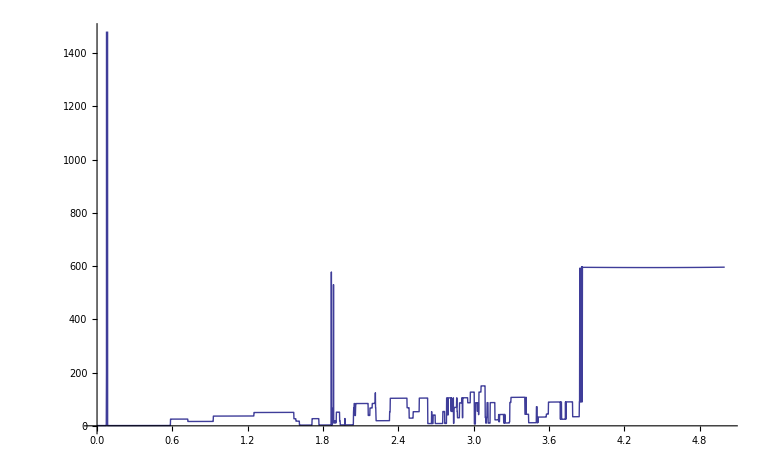
```mathematica
(*X axis is alpha, y axis is the lowest energy level*)
-Graphics-
```